```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Needs["shane`"]
```

```mathematica
SetDirectory["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs/mc-2013"];
```

```mathematica
standardErrorOfMean[list_] := Module[{n,s},s=StandardDeviation[list];
n=Length[list];
s/n^(1/2)]
```

```mathematica
meanAndDev[lists_, key_] := Map[{Mean[key /. #], standardErrorOfMean[key /. #]}&, lists]
```

```mathematica
show[lists_, key_] := Module[{},
ErrorListPlot[meanAndDev[lists, key], PlotRange -> All, AxesOrigin -> {0, 0}]]
```

```mathematica
lists1 = Map[Import["results-1/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{15,5,20,50,50,15,10,14,14,36,20,22,5,7},evalCounts→{180,60,240,600,600,180,120,168,168,432,240,264,60,84},wallClockTimes→{30.06,10.14,39.2,95.26,101.12,32.92,19.39,27.3,27.49,68.61,39.18,41.72,10.23,14.74},success→{1.,1.,1.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{28,24,7,8,10,18,1,1,18,13,36,27,27,36},evalCounts→{336,288,84,96,120,216,12,12,216,156,432,324,324,432},wallClockTimes→{86.05,59.13,16.57,18.6,23.54,48.13,2.81,2.71,43.26,32.66,88.23,60.29,66.56,84.45},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{1,1,5,1,1,1,1,1,1,1,1,1},evalCounts→{12,12,60,12,12,12,12,12,12,12,12,12},wallClockTimes→{4.92,5.25,23.21,4.99,5.06,5.02,5.11,5.05,5.,5.16,4.99,4.97},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
lists = lists1;
```

```mathematica
getSuccesses[list_, key_] := Pick[(key /. list), Map[IntegerPart,success /. list], 1 ]
```

```mathematica
synthesizeData[lists_] := lists~Join~{Map[# -> getSuccesses[lists[[1]], #]  + (# /. lists[[3]])&, {genCounts, evalCounts, wallClockTimes}]~Join~{success -> (success /. lists[[3]])~Join~Select[(success /. lists[[1]]),0. == # &] }}
```

```mathematica
synthesizeData[lists]
```

{{genCounts→{23,49,28,11,29,50,4,24,9,12,10,5,10,30,12,6,15,32,5,9},evalCounts→{276,588,336,132,348,600,48,288,108,144,120,60,120,360,144,72,180,384,60,108},wallClockTimes→{45.08,90.13,52.57,20.94,54.22,92.29,7.81,44.89,17.04,22.62,18.91,9.66,18.81,57.94,23.78,12.09,28.58,59.54,9.69,17.14},success→{1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{13,10,23,39,11,25,27,24,39,8,25,1,20,33,23,20,18,49,13,28},evalCounts→{156,120,276,468,132,300,324,288,468,96,300,12,240,396,276,240,216,588,156,336},wallClockTimes→{30.06,23.2,52.78,92.23,25.66,58.32,62.09,55.11,92.32,18.74,57.11,2.77,46.08,81.19,56.91,48.51,44.01,117.56,30.07,63.95},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{2,1,1,5,1,1,1,1,5,1,1,1,3,1,1,1,12,5,1},evalCounts→{24,12,12,60,12,12,12,12,60,12,12,12,36,12,12,12,144,60,12},wallClockTimes→{9.15,4.91,4.91,23.48,4.95,4.92,4.93,4.9,22.99,4.91,4.92,4.91,16.2,5.16,5.22,5.04,53.75,22.96,4.92},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{25,50,29,16,30,5,25,10,17,11,6,11,33,13,7,16,44,10,10},evalCounts→{300,600,348,192,360,60,300,120,204,132,72,132,396,156,84,192,528,120,120},wallClockTimes→{54.23,95.04,57.48,44.42,59.17,12.73,49.82,21.94,45.61,23.82,14.58,23.72,74.14,28.94,17.31,33.62,113.29,32.65,22.06},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.}}}

```mathematica
show[lists_, key_, opts:OptionsPattern[]] := ErrorListPlot[meanAndDev[lists, key], AxesOrigin -> {.8, 0},opts,PlotRange->Full,(*PlotRange -> {Automatic, {0, 50}}, *)AxesLabel -> {"Physics/Vehicle", key}, Ticks -> {Transpose[{{1,2,3},{"FODE", "Bullet", "FODE->Bullet"}}], Automatic}, Joined -> True]
```

```mathematica
show[lists_, key_, opts:OptionsPattern[]] := ErrorListPlot[meanAndDev[synthesizeData[lists], key], AxesOrigin -> {.8, 0},opts,PlotRange->Full,(*PlotRange -> {Automatic, {0, 50}}, *)AxesLabel -> {"Physics/Vehicle", key}, Ticks -> {Transpose[{{1,2,3, 4},{"FODE", "Bullet", "FODE->Bullet", "FODE + FODE->Bullet"}}], Automatic}, Joined -> True]
```

```mathematica
showPlus[lists, genCounts]
```

showPlus[{{genCounts→{23,49,28,11,29,50,4,24,9,12,10,5,10,30,12,6,15,32,5,9},evalCounts→{276,588,336,132,348,600,48,288,108,144,120,60,120,360,144,72,180,384,60,108},wallClockTimes→{45.08,90.13,52.57,20.94,54.22,92.29,7.81,44.89,17.04,22.62,18.91,9.66,18.81,57.94,23.78,12.09,28.58,59.54,9.69,17.14},success→{1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{13,10,23,39,11,25,27,24,39,8,25,1,20,33,23,20,18,49,13,28},evalCounts→{156,120,276,468,132,300,324,288,468,96,300,12,240,396,276,240,216,588,156,336},wallClockTimes→{30.06,23.2,52.78,92.23,25.66,58.32,62.09,55.11,92.32,18.74,57.11,2.77,46.08,81.19,56.91,48.51,44.01,117.56,30.07,63.95},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{2,1,1,5,1,1,1,1,5,1,1,1,3,1,1,1,12,5,1},evalCounts→{24,12,12,60,12,12,12,12,60,12,12,12,36,12,12,12,144,60,12},wallClockTimes→{9.15,4.91,4.91,23.48,4.95,4.92,4.93,4.9,22.99,4.91,4.92,4.91,16.2,5.16,5.22,5.04,53.75,22.96,4.92},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}},genCounts]

```mathematica
meanAndDev[lists, genCounts]
```

{{373/20,(11 √(611/19))/20},{449/20,(3 √(5771/19))/20},{45/19,(√1315)/57}}

```mathematica
checkSignificance[lists_, key_] := TableForm[{{"FODE < Bullet", MannWhitneyTest[{key /. lists[[1]] , key /. lists[[2]]}, AlternativeHypothesis->"Less"]},
{"FODE + FODE -> Bullet < Bullet", MannWhitneyTest[{getSuccesses[lists[[1]], key]  + (key /. lists[[3]]) , key /. lists[[2]]}, AlternativeHypothesis->"Less"]}}]
```

```mathematica
checkSignificanceAll[lists_] := TableForm[{{"generation count", checkSignificance[lists, genCounts]},
{"evaluation count", checkSignificance[lists, evalCounts]},
{"wall clock time", checkSignificance[lists, wallClockTimes]}}, TableSpacing->{5,2}]
```

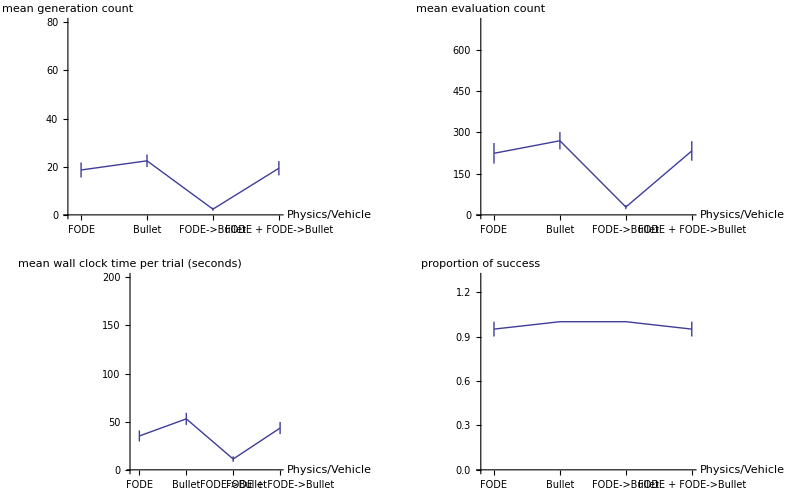

```mathematica
showAll[lists]
```

```mathematica
checkSignificanceAll[lists]
```

generation count | FODE < Bullet | 0.109106
FODE + FODE -> Bullet < Bullet | 0.152402
evaluation count | FODE < Bullet | 0.109106
FODE + FODE -> Bullet < Bullet | 0.152402
wall clock time | FODE < Bullet | 0.011135
FODE + FODE -> Bullet < Bullet | 0.090998

```mathematica
checkSignificance[lists, genCounts]
```

FODE < Bullet | 0.109106
FODE + FODE -> Bullet < Bullet | 0.152402

```mathematica
checkSignificance[lists, evalCounts]
```

FODE < Bullet | 0.109106
FODE + FODE -> Bullet < Bullet | 0.152402

```mathematica
checkSignificance[lists, wallClockTimes]
```

FODE < Bullet | 0.011135
FODE + FODE -> Bullet < Bullet | 0.090998

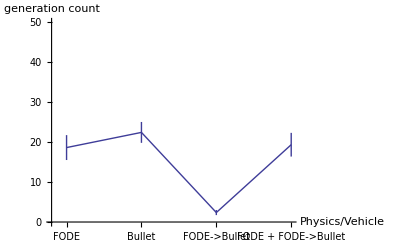

```mathematica
show[lists,genCounts, PlotRange -> {Automatic,{0, 50}}, AxesLabel -> {"Physics/Vehicle", "generation count"} ]
```

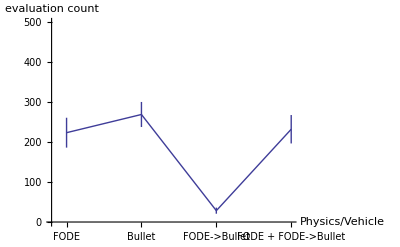

```mathematica
show[lists,evalCounts, PlotRange -> {Automatic, {0, 500}}, AxesLabel -> {"Physics/Vehicle", "evaluation count"} ]
```

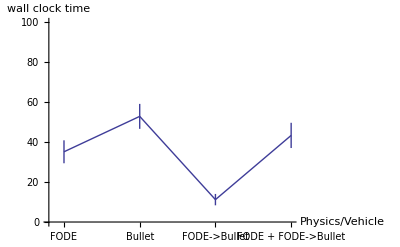

```mathematica
show[lists,wallClockTimes, PlotRange -> {Automatic, {0, 100}}, AxesLabel -> {"Physics/Vehicle",  "wall clock time"}]
```

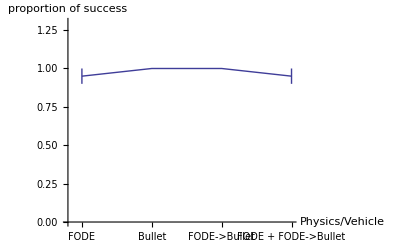

```mathematica
show[lists,success, PlotRange -> {Automatic, {0, 1.3}}, AxesLabel -> {"Physics/Vehicle", "proportion of success"}]
```

```mathematica
showAll[lists_] := GraphicsGrid[{{show[lists,genCounts, PlotRange -> {Automatic,{0, 80}}, AxesLabel -> {"Physics/Vehicle", "mean generation count"} ],
show[lists,evalCounts, PlotRange -> {Automatic, {0, 700}}, AxesLabel -> {"Physics/Vehicle", "mean evaluation count"} ]},
{show[lists,wallClockTimes, PlotRange -> {Automatic, {0, 200}}, AxesLabel -> {"Physics/Vehicle",  "mean wall clock time per trial (seconds)"}],
show[lists,success, PlotRange -> {Automatic, {0, 1.3}}, AxesLabel -> {"Physics/Vehicle", "proportion of success"}]}}]
```

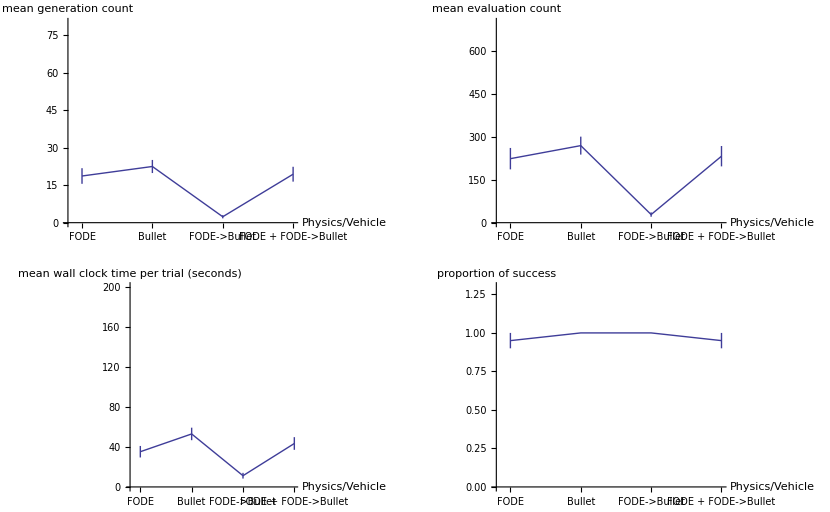

```mathematica
showAll[lists]
```

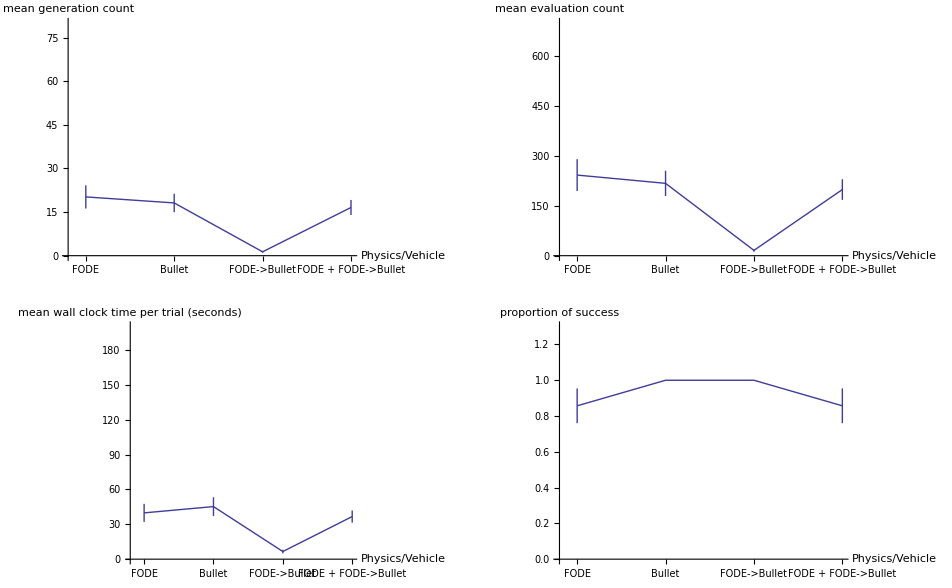

```mathematica
showAll[lists1]
```

```mathematica
lists3 = Map[Import["results-3/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{15,17,24,36,12,20,10,26,23,8,30,10,16,43,5,5,50,50,11,24},evalCounts→{180,204,288,432,144,240,120,312,276,96,360,120,192,516,60,60,600,600,132,288},wallClockTimes→{35.05,33.31,53.8,66.4,23.12,38.08,19.57,49.03,44.76,15.51,55.34,20.86,30.66,82.94,10.41,10.36,95.85,96.26,26.22,46.71},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.}},{genCounts→{50,39,50,23,50,50,50,50,16,22,32,33,50,50,50,34,50,29,50,50},evalCounts→{600,468,600,276,600,600,600,600,192,264,384,396,600,600,600,408,600,348,600,600},wallClockTimes→{178.68,118.12,165.39,61.63,130.99,131.8,132.64,131.83,37.36,51.26,74.36,93.19,126.87,143.94,153.89,84.07,157.05,74.13,150.49,148.75},success→{0.,1.,0.,1.,1.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,1.,0.,1.,0.,0.}},{genCounts→{1,1,3,1,1,2,2,2,8,1,1,6,1,1,1,14,1,3},evalCounts→{12,12,36,12,12,24,24,24,96,12,12,72,12,12,12,168,12,36},wallClockTimes→{5.96,5.04,15.71,4.93,4.93,9.56,9.59,9.38,36.28,4.9,4.87,27.52,4.97,5.11,4.99,65.79,7.47,14.85},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
lists6 = Map[Import["results-6/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{26,13,50,49,22,50,12,4,2,35,11,37,50,38,34,13,10,36,30,50},evalCounts→{312,156,600,588,264,600,144,48,24,420,132,444,600,456,408,156,120,432,360,600},wallClockTimes→{48.64,24.92,95.01,92.8,42.66,93.21,22.97,7.96,4.24,67.37,21.02,69.6,92.04,70.14,65.29,24.27,19.3,71.4,59.29,94.62},success→{1.,1.,0.,1.,1.,0.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,0.}},{genCounts→{50,30,43,50,50,50,50,9,25,50,50,37,31,7,50,50,50,37,50,30},evalCounts→{600,360,516,600,600,600,600,108,300,600,600,444,372,84,600,600,600,444,600,360},wallClockTimes→{166.6,71.75,115.54,132.79,132.64,128.52,128.83,21.88,59.55,132.23,126.95,93.07,72.81,17.37,126.43,130.5,128.1,87.27,137.74,73.28},success→{0.,1.,1.,0.,0.,0.,0.,1.,1.,0.,0.,1.,1.,1.,0.,0.,0.,1.,0.,1.}},{genCounts→{50,12,5,50,19,1,2,50,50,50,50,50,6,3,1,19},evalCounts→{600,144,60,600,228,12,24,600,600,600,600,600,72,36,12,228},wallClockTimes→{181.86,38.11,16.63,164.2,58.02,3.56,6.69,163.54,156.85,164.82,161.17,158.49,19.97,9.44,3.57,60.68},success→{0.,1.,1.,0.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.,1.}}}

```mathematica
lists7 = Map[Import["results-7/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{1,14,21,47,14,4,8,45,11,14,14,34,8,48,19,20,15,5,6,21,11,2,39,17,7,50,32,1,23,24,8,28,6,12,9,15,50,25,16,9},evalCounts→{12,168,252,564,168,48,96,540,132,168,168,408,96,576,228,240,180,60,72,252,132,24,468,204,84,600,384,12,276,288,96,336,72,144,108,180,600,300,192,108},wallClockTimes→{2.3,28.69,47.8,119.28,30.62,9.46,18.71,100.81,23.62,28.82,32.64,65.3,18.63,110.36,36.49,37.8,29.29,9.78,12.78,39.97,22.51,4.17,77.25,32.01,13.71,93.73,61.32,2.32,46.1,47.69,16.11,54.77,11.86,23.89,17.69,30.1,105.89,51.51,39.47,21.14},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.}},{genCounts→{50,14,50,50,15,50,1,50,50,12,49,50,50,50,50,12,49,11,50,39,50,50,25,16,17,50,50,32,50,50,50,50,36,36,6,16,24,50,50,22},evalCounts→{600,168,600,600,180,600,12,600,600,144,588,600,600,600,600,144,588,132,600,468,600,600,300,192,204,600,600,384,600,600,600,600,432,432,72,192,288,600,600,264},wallClockTimes→{120.76,39.04,141.11,145.66,40.65,139.15,3.95,142.22,133.66,31.32,135.76,120.1,142.91,126.67,117.16,28.54,115.45,26.56,124.39,91.95,123.53,116.68,62.92,37.51,41.05,117.55,117.28,74.99,116.2,124.9,138.31,120.29,91.15,85.01,16.27,39.85,60.59,127.89,136.1,80.08},success→{0.,1.,0.,0.,1.,0.,1.,1.,0.,1.,1.,0.,0.,0.,0.,1.,1.,1.,0.,1.,0.,0.,1.,1.,1.,0.,0.,1.,0.,0.,0.,0.,1.,1.,1.,1.,1.,0.,0.,1.}},{genCounts→{50,23,32,17,35,50,7,50,50,43,50,50,50,50,9,50,5,13,50,42,32,50,16,42,44,2,50,50,27,50,4,11,50,44,50,50,50,1},evalCounts→{600,276,384,204,420,600,84,600,600,516,600,600,600,600,108,600,60,156,600,504,384,600,192,504,528,24,600,600,324,600,48,132,600,528,600,600,600,12},wallClockTimes→{154.09,85.69,118.23,79.08,139.73,186.66,24.04,169.81,168.48,142.39,172.92,164.3,181.55,149.71,27.53,150.08,16.2,40.11,154.82,132.23,97.76,148.6,48.39,125.39,131.62,6.64,151.32,166.92,89.26,152.03,13.43,33.82,160.7,143.6,158.58,182.87,180.8,6.66},success→{0.,1.,1.,1.,1.,0.,1.,0.,0.,1.,0.,0.,0.,0.,1.,0.,1.,1.,0.,1.,1.,0.,1.,1.,1.,1.,0.,0.,1.,0.,1.,1.,0.,1.,0.,0.,0.,1.}}}

```mathematica
lists8b = Map[Import["results-8/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{11,15,7,4,17,24,50,25,16,21,19,7,20,7,19,29,13,42,13,19,17,30,21,2,11,38,15,19,50,11,8,24,50,2,12},evalCounts→{132,180,84,48,204,288,600,300,192,252,228,84,240,84,228,348,156,504,156,228,204,360,252,24,132,456,180,228,600,132,96,288,600,24,144},wallClockTimes→{21.05,27.8,13.07,7.74,31.59,45.89,104.92,47.63,29.65,40.8,36.,13.71,38.6,13.11,34.78,52.78,24.02,77.87,25.05,37.44,33.62,54.73,38.52,4.16,22.98,70.73,28.1,35.32,93.92,21.81,16.01,46.82,94.54,4.95,22.32},success→{1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,0.,1.,1.}},{genCounts→{14,16,6,48,50,50,14,21,41,24,30,50,6,39,8,43,10,18,24,3,6,16,27,6,20,25,5,13,50,1,20,13,15,10,50},evalCounts→{168,192,72,576,600,600,168,252,492,288,360,600,72,468,96,516,120,216,288,36,72,192,324,72,240,300,60,156,600,12,240,156,180,120,600},wallClockTimes→{32.19,34.75,13.58,103.24,110.92,110.16,35.52,49.13,93.93,54.07,67.4,116.37,13.97,84.5,17.86,93.11,22.23,39.16,54.7,7.68,14.67,35.25,61.57,15.2,56.93,55.22,11.73,29.04,118.8,2.88,44.25,29.3,33.59,23.08,114.4},success→{1.,1.,1.,1.,0.,0.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,0.}},{genCounts→{6,1,44,50,9,1,50,19,16,50,50,14,50,4,37,4,50,13,1,50,15,13,22,1,1,3,22,11,1,3,9,50},evalCounts→{72,12,528,600,108,12,600,228,192,600,600,168,600,48,444,48,600,156,12,600,180,156,264,12,12,36,264,132,12,36,108,600},wallClockTimes→{19.66,3.27,121.52,142.5,26.17,3.5,148.89,54.6,45.26,148.84,148.76,44.88,139.22,11.73,102.7,11.76,145.5,40.82,3.7,144.68,42.44,37.65,73.54,3.27,3.35,9.29,66.37,34.81,3.57,9.26,27.97,144.},success→{1.,1.,1.,0.,1.,1.,0.,1.,1.,0.,0.,1.,0.,1.,1.,1.,0.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.}}}

```mathematica
lists10 = Map[Import["results-10/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{12,35,50,18,21,13,13,35,31,13},evalCounts→{144,420,600,216,252,156,156,420,372,156},wallClockTimes→{28.76,82.26,120.85,43.53,51.28,32.76,31.07,84.16,75.01,30.85},success→{1.,1.,0.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{19,24,24,5,24,23,13,29,2,5},evalCounts→{228,288,288,60,288,276,156,348,24,60},wallClockTimes→{55.78,61.8,68.58,13.77,72.26,64.51,35.18,78.26,5.71,13.44},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{50,4,50,12,28,16,3,50,50},evalCounts→{600,48,600,144,336,192,36,600,600},wallClockTimes→{168.81,13.64,169.85,41.07,97.36,55.63,10.61,165.47,164.58},success→{0.,1.,0.,1.,1.,1.,1.,0.,0.}}}

```mathematica
lists11 = Map[Import["results-11/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{12,4,12,3,50,5,30,43,36,10,9,12,14,16,21,40,26,14,19,13},evalCounts→{144,48,144,36,600,60,360,516,432,120,108,144,168,192,252,480,312,168,228,156},wallClockTimes→{28.73,10.64,31.91,7.66,126.33,12.86,74.21,106.05,99.45,25.56,23.15,29.04,42.07,38.17,50.68,96.14,61.52,33.57,53.04,32.34},success→{1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{50,41,50,43,42,50,50,49,26,50,50,50,50,10,23,50,50,50,50,50},evalCounts→{600,492,600,516,504,600,600,588,312,600,600,600,600,120,276,600,600,600,600,600},wallClockTimes→{157.98,131.33,166.64,142.12,148.81,171.26,159.1,180.64,95.62,173.14,162.99,150.99,187.87,30.45,72.77,152.82,152.3,149.28,159.77,153.97},success→{0.,1.,0.,1.,1.,0.,0.,1.,1.,0.,0.,0.,0.,1.,1.,0.,0.,0.,0.,0.}},{genCounts→{34,50,50,15,2,29,50,41,10,24,4,50,7,12,11,6,6,50,1},evalCounts→{408,600,600,180,24,348,600,492,120,288,48,600,84,144,132,72,72,600,12},wallClockTimes→{148.46,239.2,246.19,68.29,9.59,135.84,230.83,235.86,48.9,123.13,18.19,277.56,38.21,52.17,48.08,26.75,26.53,226.3,4.95},success→{1.,0.,0.,1.,1.,1.,0.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,0.,1.}}}

```mathematica
checkSignificance[lists3, genCounts]
```

FODE < Bullet | 0.000065151
FODE + FODE -> Bullet < Bullet | 0.0000107558

```mathematica
checkSignificance[lists3, evalCounts]
```

FODE < Bullet | 0.000065151
FODE + FODE -> Bullet < Bullet | 0.0000107558

```mathematica
checkSignificance[lists3, wallClockTimes]
```

FODE < Bullet | 1.99368×10^-6
FODE + FODE -> Bullet < Bullet | 7.07769×10^-6

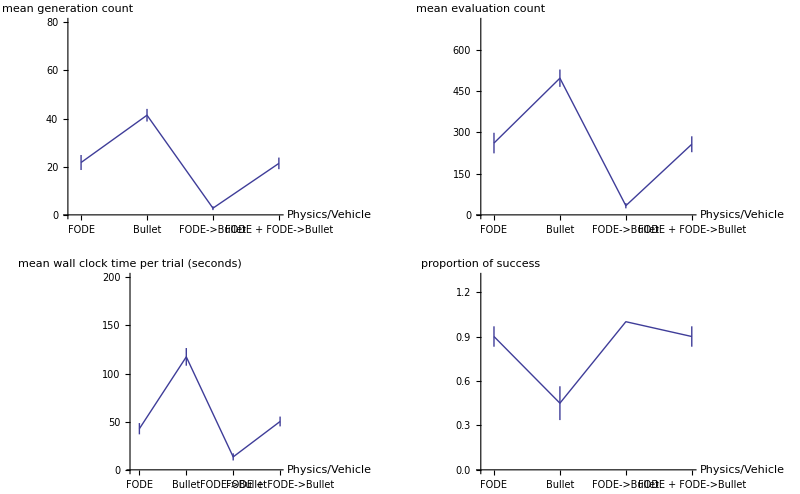

```mathematica
showAll[lists3]
```

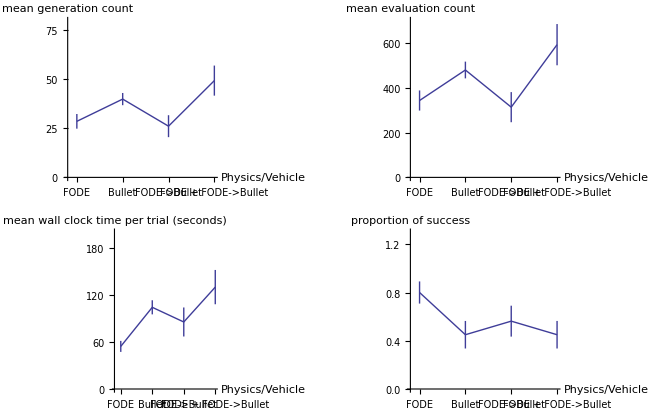

```mathematica
showAll[lists6]
```

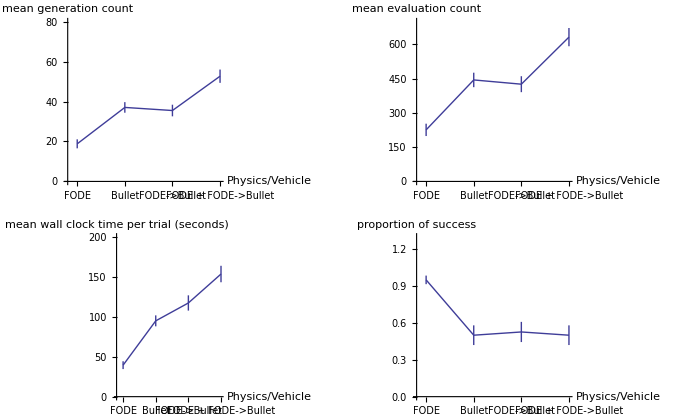

```mathematica
showAll[lists7]
```

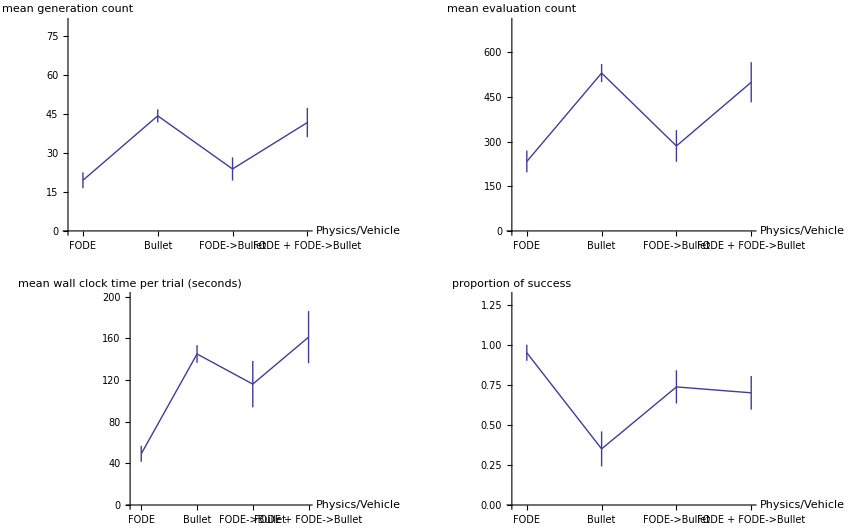

```mathematica
showAll[lists11]
```

```mathematica
checkSignificanceAll[lists11]
```

generation count | FODE < Bullet | 4.96504×10^-6
FODE + FODE -> Bullet < Bullet | 0.398321
evaluation count | FODE < Bullet | 4.96504×10^-6
FODE + FODE -> Bullet < Bullet | 0.398321
wall clock time | FODE < Bullet | 6.88031×10^-7
FODE + FODE -> Bullet < Bullet | 0.405619

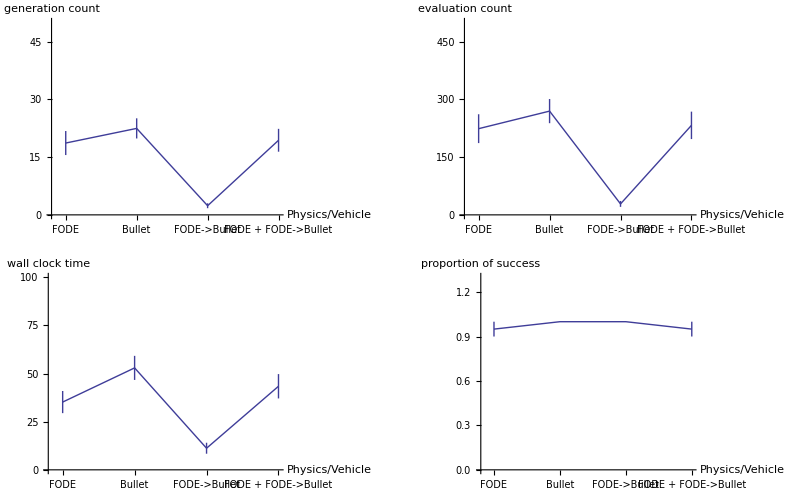

```mathematica
GraphicsGrid[{{show[lists,genCounts, PlotRange -> {Automatic,{0, 50}}, AxesLabel -> {"Physics/Vehicle", "generation count"} ],
show[lists,evalCounts, PlotRange -> {Automatic, {0, 500}}, AxesLabel -> {"Physics/Vehicle", "evaluation count"} ]},
{show[lists,wallClockTimes, PlotRange -> {Automatic, {0, 100}}, AxesLabel -> {"Physics/Vehicle",  "wall clock time"}],
show[lists,success, PlotRange -> {Automatic, {0, 1.3}}, AxesLabel -> {"Physics/Vehicle", "proportion of success"}]}}]
```